# Computer Mathematics Course Work

Dmytro Zakharov

Kharkiv Karazin National University, Applied Mathematics

Variant 13

## 1. Introduction to Wolfram Mathematica

### 1.1. Arithmetical Operations

Task: Find value of expression (0.134+0.05)/((18+1/6)-(1+11/14)-2/15 (2+6/7))

```mathematica
Clear[Answer]
Answer = (0.134+0.05)/((18+1/6)-(1+11/14)-2/15(2+6/7));
Print["Answer is ", Answer]
```

Answer is 0.0115

### 1.2. Evaluating expression containing solely elementary functions

Task: Find the value of expression

```mathematica
Clear[y,Answer]
y=1/3 Cos[1/Tan[3]]+1/5 (Sin[5 Sqrt[2]])^2/Cos[10 ⅇ^3];
Answer = N[y];
Print["Answer is ", Answer]
```

Answer is 0.350611

## 2. Algebraic Evaluation

### 2.1. Algebraic Manipulations

Task: Simplify expression

```mathematica
Clear[a,b,c,n,Result]
Result=Simplify[((2 a^2(b+c)^(2n)-1/2)/(a n^2-a^3-2 a^2-a))/((2a(b+c)^n-1)/(a^2 c-a(n c-c)))];
Print["Result is ", Result]
```

Result is -(c (1+2 a (b+c)^n))/(2 (1+a+n))

### 2.2. Finding values of algebraic expressions

Task: Calculate  for

```mathematica
Remove[a,b,Answer]
Expr = (Sqrt[a b]-(a b)/(a+Sqrt[a b]))/((Surd[a b,4]-Sqrt[b])/(a-b));
Answer = Simplify[Expr/.{a->8,b->2}];
Print["The answer is ", Answer]
```

The answer is 8 (2+√2)

### 2.3. Solving equations

Task: Solve equation  for

```mathematica
Clear[a,x]
Solve[1/a+1/(a+x)+1/(a+2 x)==0,x]
```

{{x→1/2 (-3 a-√3 a)},{x→1/2 (-3 a+√3 a)}}

## 3. Elements of Analytical Geometry

### 3.1. Operating with vectors

Task: For vectors  determine whether  and  are collinear. Find lengths of vectors  and  and angle between them. Draw vectors  and .

```mathematica
Clear[a,b,c1,c2]
a={-2,7,-1};
b={-3,5,2};
c1=2 a+3 b;
c2=3a+2b;
ratio=c1/c2;
Print["Ratio is ", ratio]
```

Ratio is {13/12,29/31,4}

We thus conclude that  and  are not collinear.

```mathematica
LengthOfA=Norm[a];
LengthOfB=Norm[b];
AngleAB=(N[VectorAngle[a,b]] 180)/π;
Print["Length of a is ", LengthOfA," and length of b is ", LengthOfB]
Print["Angle between a and b (in degrees) is ", AngleAB]
```

Length of a is Norm[a] and length of b is Norm[b]

Angle between a and b (in degrees) is (180 VectorAngle[a,b])/π

```mathematica
z={0,0,0}
Graphics3D[{Thickness[0.02],Arrowheads[0.1],Arrow[{z,a}],Arrow[{z,b}]},Axes->True,AxesLabel->{"x","y","z"}]
```

{0,0,0}

-Graphics3D-

### 3.2. Geometric calculations in Triangle

Task: Given triangle with vertices , find its sides, angles and area.

```mathematica
A1 = {6,2,-3}; A2 = {6,3,-2}; A3={7,3,-3};
ListPlot3D[{A1,A2,A3},BoxRatios->Automatic,ColorFunction->"SouthwestColors"]
```

-Graphics3D-

```mathematica
A1A2=A2-A1; A1A3=A3-A1; A2A3=A3-A2;
LengthA1A2=Norm[A1A2];LengthA1A3=Norm[A1A3];LengthA2A3=Norm[A2A3];
angleA1=VectorAngle[A1A2,A1A3];angleA2=VectorAngle[-A1A2,A2A3]; angleA3=VectorAngle[A1A3,A2A3];
Print["Lengths of sides A_1A_2, A_1A_3, and A_2A_3 are ", LengthA1A2,", ",LengthA1A3,", ",LengthA2A3]
Print["Angles A_1, A_2, and A_3 are ", angleA1, ", ", angleA2,", ", angleA3]
```

Lengths of sides A_1A_2, A_1A_3, and A_2A_3 are √2, √2, √2

Angles A_1, A_2, and A_3 are π/3, π/3, π/3

```mathematica
S=1/2 Norm[Cross[A1A2,A1A3]];
Print["Area of triangle is ", S]
```

Area of triangle is (√3)/2

### 3.3. Calculations in Tetrahedron

Task. Given Tetrahedron with vertices , find its volume, height  from vertex  on side . Display this tetrahedron, height  and point .

```mathematica
A1={1,1,2};A2={-1,1,3};A3={2,-2,4};A4={-1,0,-2};
A1A2=A2-A1;A1A3=A3-A1;A1A4=A4-A1;
V=1/6 Abs[Det[{A1A2,A1A3,A1A4}]];
n=-Cross[A1A2,A1A3];
S=1/2 Norm[n];
h=(3 V)/S;
B=A4-n/(2S)h;
graph1=Graphics3D[{Thickness[0.01],Line[{A1,A2,A3,A1,A4,A2,A3,A4}]},AxesLabel->{"x","y","z"},Axes->True,BaseStyle->{Blue,Opacity[.7]}];
graph2=ListPointPlot3D[{B}->{"Intersection"},PlotStyle->{Directive[PointSize[0.03],Red]}];
graph3=Graphics3D[{Thickness[0.01],{Dashed,Red,Line[{A4,B}]}}];
graph4=Graphics3D[{Opacity[0.3],Gray,InfinitePlane[{A1,A2,A3}]}];
Show[graph1,graph2,graph3,graph4]
```

-Graphics3D-

## 4. Matrix Calculations

### 4.1. Working with matrices

Task: Given matrices , find  where  is an identity matrix. Find inverse matrix . Find . Find sum and difference of . Find  and , find difference between these values. Solve matrix equation  with respect to .

```mathematica
A={{1,2,1},{0,2,0},{-1,1,1}};
B={{1,1,2},{0,2,1},{1,-1,0}};
M=2*A.A+3 A+5 IdentityMatrix[3];
Print["Matrix polynomial equals ",M//MatrixForm]
```

Matrix polynomial equals (8 | 20 | 7
0 | 19 | 0
-7 | 5 | 8)

```mathematica
InverseA=Inverse[A];
Print["Inverse of matrix A is ", InverseA//MatrixForm]
```

Inverse of matrix A is (1/2 | -1/4 | -1/2
0 | 1/2 | 0
1/2 | -3/4 | 1/2)

```mathematica
DetA=Det[A];
Print["det(A) = ", DetA]
```

det(A) = 4

```mathematica
Print["Sum of matrices A and B is ", (A+B)//MatrixForm]
Print["Difference between matrices A and B is ", (A-B)//MatrixForm]
```

Sum of matrices A and B is (2 | 3 | 3
0 | 4 | 1
0 | 0 | 1)

Difference between matrices A and B is (0 | 1 | -1
0 | 0 | -1
-2 | 2 | 1)

```mathematica
MatProduct=A.B;
ElemProduct=A*B;
Print["Matrix product of A and B is ", MatProduct//MatrixForm]
Print["Elementwise product of A and B is ", ElemProduct//MatrixForm]
Print["Difference between corresponding products is", (MatProduct-ElemProduct)//MatrixForm]
```

Matrix product of A and B is (2 | 4 | 4
0 | 4 | 2
0 | 0 | -1)

Elementwise product of A and B is (1 | 2 | 2
0 | 4 | 0
-1 | -1 | 0)

Difference between corresponding products is(1 | 2 | 2
0 | 0 | 2
1 | 1 | -1)

```mathematica
X=InverseA.B;
Print["Solution to matrix equation AX=B w/ respect to X is ", X//MatrixForm]
```

Solution to matrix equation AX=B w/ respect to X is (0 | 1/2 | 3/4
0 | 1 | 1/2
1 | -3/2 | 1/4)

### 4.2. Working with both matrices and vectors

Task: Given matrices  calculate  and . Solve equation  with respect to  using inverse matrix and Cramer’s rule. For each row and column of  find sum of elements. For matrix  find max and min elements.

```mathematica
A={{0,2,3},{4,1,0},{2,-1,-2}};
B={{1,2,0},{3,0,-1},{2,1,-1}};
x={2,4,-1};
y=(A-B).(A-B).x;
Print["Vector y is ", MatrixForm[y]]
z=(A.B-B.A).x;
Print["Vector z is ", MatrixForm[z]]
```

Vector y is (-16
-7
-3)

Vector z is (12
34
-25)

To solve equation  we firstly use inverse matrix, that is, :

```mathematica
u=Inverse[A].x;
Print["Solution to Au=x w/ respect to u is ",MatrixForm[u]]
```

Solution to Au=x w/ respect to u is (-3/2
10
-6)

Now, using Cramer’s rule:

```mathematica
A1=Join[Transpose[{x}],A[[All,2;;3]],2];
Print["After putting vector x to the first column we get ",MatrixForm[A1]]
```

After putting vector x to the first column we get (2 | 2 | 3
4 | 1 | 0
-1 | -1 | -2)

```mathematica
A2=Join[A[[All,1;;1]],Transpose[{x}],A[[All,3;;3]],2];
Print["After putting vector x to the second column we get ",MatrixForm[A2]]
```

After putting vector x to the second column we get (0 | 2 | 3
4 | 4 | 0
2 | -1 | -2)

```mathematica
A3=Join[A[[All,1;;2]],Transpose[{x}],2];
Print["After putting vector x to the third column we get ",MatrixForm[A3]]
```

After putting vector x to the third column we get (0 | 2 | 2
4 | 1 | 4
2 | -1 | -1)

```mathematica
cramerU={Det[A1],Det[A2],Det[A3]}/Det[A];
Print["Vector u calculated using Cramer's rule is ", cramerU//MatrixForm]
```

Vector u calculated using Cramer's rule is (-3/2
10
-6)

```mathematica
Print["Sum of columns of matrix A is ",Total[A]]
Print["Sum of rows of matrix A is ", Total[A,{2}]]
Print["Max element of B is ",Max[B]]
Print["Min element of B is ",Min[B]]
```

Sum of columns of matrix A is {6,2,1}

Sum of rows of matrix A is {5,5,-1}

Max element of B is 3

Min element of B is -1

### 4.3. Creating matrices

Task 1: Generate a one-dimensional array  of size  containing random real numbers. Sort it in descending order and convert to a matrix . Create matrix  of size  containing ’s. Generate matrix  of size , elements  of which are calculated according to formula . Generate diagonal array  with elements of diagonal . Calculate  where  is identity matrix of size .

```mathematica
a=RandomReal[1,16];
Print["Random list a is ",a]
aSorted=Sort[a,Greater];
Print["Sorted list a is ",aSorted]
A=ArrayReshape[aSorted,{4,4}];
Print["Reshaped list a as a matrix A is ", A//MatrixForm]
B=ConstantArray[5,{4,4}];
Print["Matrix B is ",B//MatrixForm]
F=Table[i^2-j^2,{i,1,4},{j,1,4}];
Print["Matrix F is ",F//MatrixForm]
G=DiagonalMatrix[{1,-1,2,-2}];
Print["Matrix G is ", G//MatrixForm];
M=A+B-F-G+IdentityMatrix[4]-3;
Print["Expression A+B-F-G+E-3 equals ",M//MatrixForm]
```

Random list a is {0.35427,0.699043,0.911459,0.477622,0.589589,0.200876,0.154128,0.557092,0.580649,0.758855,0.807006,0.961893,0.419614,0.473136,0.863843,0.452541}

Sorted list a is {0.961893,0.911459,0.863843,0.807006,0.758855,0.699043,0.589589,0.580649,0.557092,0.477622,0.473136,0.452541,0.419614,0.35427,0.200876,0.154128}

Reshaped list a as a matrix A is (0.961893 | 0.911459 | 0.863843 | 0.807006
0.758855 | 0.699043 | 0.589589 | 0.580649
0.557092 | 0.477622 | 0.473136 | 0.452541
0.419614 | 0.35427 | 0.200876 | 0.154128)

Matrix B is (5 | 5 | 5 | 5
5 | 5 | 5 | 5
5 | 5 | 5 | 5
5 | 5 | 5 | 5)

Matrix F is (0 | -3 | -8 | -15
3 | 0 | -5 | -12
8 | 5 | 0 | -7
15 | 12 | 7 | 0)

Matrix G is (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | -2)

Expression A+B-F-G+E-3 equals (2.96189 | 5.91146 | 10.8638 | 17.807
-0.241145 | 4.69904 | 7.58959 | 14.5806
-5.44291 | -2.52238 | 1.47314 | 9.45254
-12.5804 | -9.64573 | -4.79912 | 5.15413)

Task 2. Create matrix  elements of which are calculated according to relation  where . Add to  a column containing . Then, between columns 1 and 2 insert another column containing ’s.

```mathematica
x={-3,0,1,2,5};y={-5,0,-4,1,3};
Z=Table[(x[[i]])^2-(y[[j]])^2,{i,1,5},{j,1,5}];
Print["Initial matrix Z is ", Z//MatrixForm]
```

Initial matrix Z is (-16 | 9 | -7 | 8 | 0
-25 | 0 | -16 | -1 | -9
-24 | 1 | -15 | 0 | -8
-21 | 4 | -12 | 3 | -5
0 | 25 | 9 | 24 | 16)

```mathematica
joinedZ=Join[Z,Transpose[{{1,2,3,4,5}}],2];
Print["After adding columns {1,2,3,4,5} to Z we get ",joinedZ//MatrixForm]
```

After adding columns {1,2,3,4,5} to Z we get (-16 | 9 | -7 | 8 | 0 | 1
-25 | 0 | -16 | -1 | -9 | 2
-24 | 1 | -15 | 0 | -8 | 3
-21 | 4 | -12 | 3 | -5 | 4
0 | 25 | 9 | 24 | 16 | 5)

```mathematica
joinedWithOnesZ=Join[joinedZ[[All,1;;1]],Transpose[{ConstantArray[1,5]}],joinedZ[[All,3;;6]],2];
Print["After adding column {1,1,1,1,1} between first and second solumns we get ", joinedWithOnesZ//MatrixForm]
```

After adding column {1,1,1,1,1} between first and second solumns we get (-16 | 1 | -7 | 8 | 0 | 1
-25 | 1 | -16 | -1 | -9 | 2
-24 | 1 | -15 | 0 | -8 | 3
-21 | 1 | -12 | 3 | -5 | 4
0 | 1 | 9 | 24 | 16 | 5)

## 5. Solving equations and systems of equations

### 5.1. Solving equations

Task. Solve equation  w/ respect to .

```mathematica
Clear[x,a]
Solve[(Sqrt[1+x^2/a^2]-x/a)/(Sqrt[1+x^2/a^2]+x/a)==1/4,x]
```

{{x→(3 a)/4}}

### 5.2. Solving system of linear equations

Task. Solve system of linear equations  given my matrix  and vector .

#### 5.2.1. Inverse matrix method

```mathematica
Clear[A,b,x];
A={{1,2,-3,4,-1},{2,-1,3,-4,2},{3,1,-1,2,-1},{4,3,4,2,2},{1,-1,-1,2,-3}};
b={-1,8,3,-2,-3};
x=Inverse[A].b;
Print["x = ",x]
```

x = {2,0,-2,-2,1}

#### 5.2.2. Using Solve function

```mathematica
Solve[x1+2x2-3x3+4x4-x5==-1&&2x1-x2+3x3-4x4+2x5==8&&3x1+x2-x3+2x4-x5==3&&4x1+3x2+4x3+2x4+2x5==-2&&x1-x2-x3+2x4-3x5==-3,{x1,x2,x3,x4,x5}]
```

{{x1→2,x2→0,x3→-2,x4→-2,x5→1}}

#### 5.2.3. Using LinearSolve function

```mathematica
Clear[A,b,x];
A={{1,2,-3,4,-1},{2,-1,3,-4,2},{3,1,-1,2,-1},{4,3,4,2,2},{1,-1,-1,2,-3}};
b={-1,8,3,-2,-3};
x=LinearSolve[A,b];
Print["x = ",x]
```

x = {2,0,-2,-2,1}

#### 5.2.4. Using Cramer’s method

```mathematica
Clear[A,b,x];
A={{1,2,-3,4,-1},{2,-1,3,-4,2},{3,1,-1,2,-1},{4,3,4,2,2},{1,-1,-1,2,-3}};
b={-1,8,3,-2,-3};
A1=Join[Transpose[{b}],A[[All,2;;5]],2];
A2=Join[A[[All,1;;1]],Transpose[{b}],A[[All,3;;5]],2];
A3=Join[A[[All,1;;2]],Transpose[{b}],A[[All,4;;5]],2];
A4=Join[A[[All,1;;3]],Transpose[{b}],A[[All,5;;5]],2];
A5=Join[A[[All,1;;4]],Transpose[{b}],2];
x={Det[A1],Det[A2],Det[A3],Det[A4],Det[A5]}/Det[A];
Print["x = ",x]
```

x = {2,0,-2,-2,1}

#### 5.2.5. Using RowReduce method

```mathematica
Clear[A,b,x];
A={{1,2,-3,4,-1},{2,-1,3,-4,2},{3,1,-1,2,-1},{4,3,4,2,2},{1,-1,-1,2,-3}};
b={-1,8,3,-2,-3};
RowReduce[Join[A,Transpose[{b}],2]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 2
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | -2
0 | 0 | 0 | 1 | 0 | -2
0 | 0 | 0 | 0 | 1 | 1)

### 5.3. Solving non-linear equations

Task. Solve system of non-linear equations  and .

```mathematica
Clear[x,y]
Solve[x^3+y^3==35&&x y(x+y) == 30,{x,y},Reals]
```

{{x→2,y→3},{x→3,y→2}}

## 6. Functions and their plots

### 6.1. Plotting function by a points list

Task. Plot function  and its table of values. Plot ListPlot based on this table.

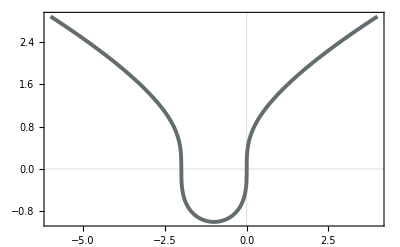

```mathematica
Remove[x,y];
y[x_]=CubeRoot[x(x+2)];
p1=Plot[y[x],{x,-6,4},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

```mathematica
points=Table[{x,N[y[x]]},{x,-6,4,0.5}];
points//TableForm
```

-6. | 2.8845
-5.5 | 2.68005
-5. | 2.46621
-4.5 | 2.2407
-4. | 2.
-3.5 | 1.73801
-3. | 1.44225
-2.5 | 1.07722
-2. | 0.
-1.5 | -0.90856
-1. | -1.
-0.5 | -0.90856
0. | 0.
0.5 | 1.07722
1. | 1.44225
1.5 | 1.73801
2. | 2.
2.5 | 2.2407
3. | 2.46621
3.5 | 2.68005
4. | 2.8845

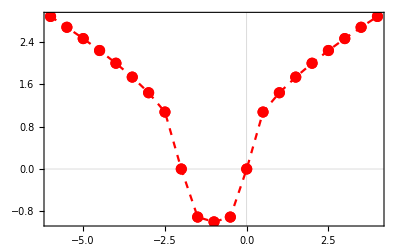

```mathematica
p2=ListPlot[points,Joined->True,Mesh->Full,PlotStyle->{PointSize[0.02],Red,Dashed},PlotTheme->"Scientific"]
```

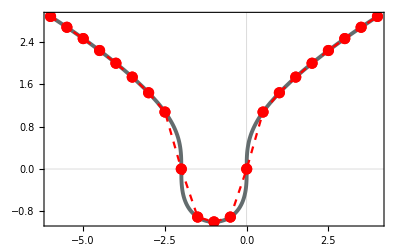

```mathematica
Show[p1,p2]
```

### 6.2. Building polynomial plot

Task. Plot polynomial .

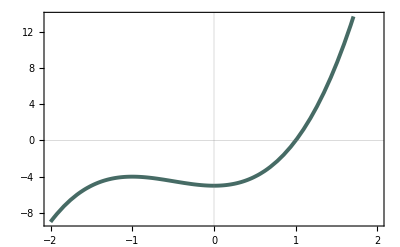

```mathematica
Remove[x,y];
y[x_]=-5+3 x^2+2 x^3;
Plot[y[x],{x,-2,2},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

### 6.3. Build arbitrary explicitly defined function

Task. Plot

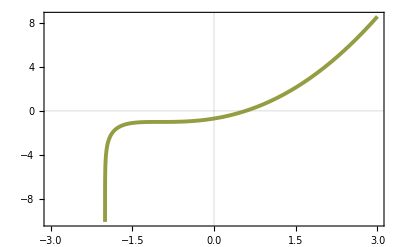

```mathematica
Clear[x,y];
y[x_]=2 x+x^2-(x+1)Log[x+2];
Plot[y[x],{x,-3,3},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

### 6.4. Drawing Parametric Plots

Task. Build function . Build table of values on interval  and corresponding list plot.

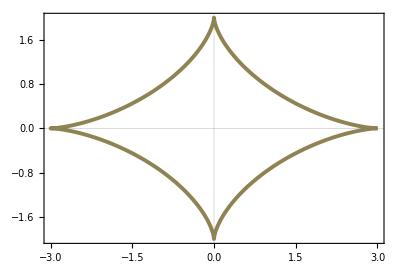

```mathematica
Remove[x,y,t];
x[t_]=3(Cos[t])^3;
y[t_]=2(Sin[t])^3;
p1=ParametricPlot[{x[t],y[t]},{t,0,2π},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007],Blue},ColorFunction->"DarkRainbow"]
```

```mathematica
points=Table[{x[t],y[t]},{t,0,2π,π/8}];
npoints=N[points];
npoints//TableForm
```

3. | 0.
2.36574 | 0.112085
1.06066 | 0.707107
0.168128 | 1.57716
0. | 2.
-0.168128 | 1.57716
-1.06066 | 0.707107
-2.36574 | 0.112085
-3. | 0.
-2.36574 | -0.112085
-1.06066 | -0.707107
-0.168128 | -1.57716
0. | -2.
0.168128 | -1.57716
1.06066 | -0.707107
2.36574 | -0.112085
3. | 0.

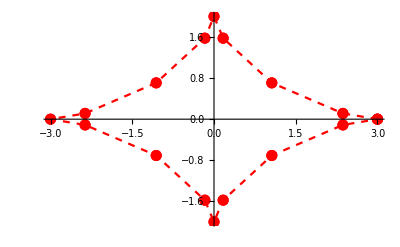

```mathematica
p2=ListPlot[npoints,Joined->True,Mesh->Full,PlotStyle->{PointSize[0.02],Red,Dashed}]
```

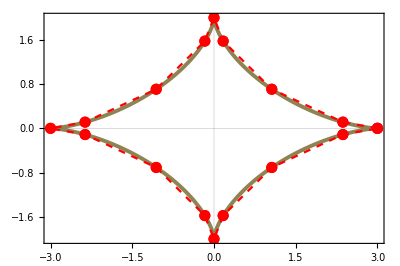

```mathematica
Show[p1,p2]
```

### 6.5. Drawing parametric plots

Task. Build plot  for interval .

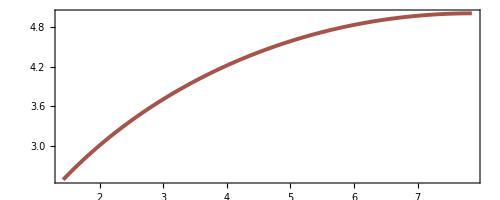

```mathematica
Clear[x,y,t]
x[t_]=5/2(t-Sin[t]);
y[t_]=5/2(1-Cos[t]);
p1=ParametricPlot[{x[t],y[t]},{t,π/2,π},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

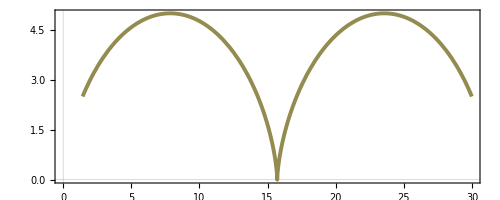

```mathematica
p2=ParametricPlot[{x[t],y[t]},{t,π/2,(7π)/2},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

### 6.6. Build unexplicitly defined functions

Task. Build curve

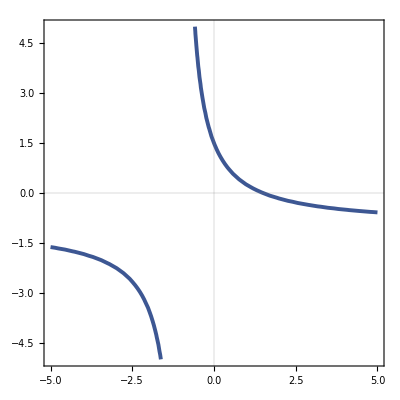

```mathematica
Remove[x,y,F];
F[x_,y_]=2x y+2x+2y-3;
ContourPlot[F[x,y]==0,{x,-5,5},{y,-5,5},PlotTheme->"Scientific",ColorFunction->"DarkRainbow",ContourStyle->{Thickness[0.007]}]
```

## 7. Geometric objects

### 7.1. Building a plane based on three points

Task: Write down an equation of plane intersecting points . Display this plane and three points.

```mathematica
Clear[A1,A2,A3,x,y,z];
A1={-3,-5,6};A2={2,1,-4};A3={0,-3,-1};
p1=ListPointPlot3D[{A1,A2,A3}->{"A_1","A_2","A_3"},PlotStyle->{Directive[PointSize[0.03],Red]}];
r={x,y,z};
Eq=Det[{r-A1,A2-A1,A3-A1}];
Print["Plane equation is ",Eq == 0]
```

Plane equation is 7-22 x+5 y-8 z==0

```mathematica
p2=ContourPlot3D[Eq==0,{x,-7,5},{y,-7,5},{z,-5,7},ContourStyle->Directive[Opacity[0.5],Blue]];
Show[p2,p1,PlotRange->All,AspectRatio->Automatic]
```

-Graphics3D-

### 7.2. Parallelogram in R^3

Task: In  three vertices of parallelogram  are given. Find coordinate of the fourth vertex  which is opposite to the side . Find area of this parallelogram. Display contours of this parallelogram and its vertices.

```mathematica
A1={6,2,-3};A2={6,3,-2};A3={7,3,-3};
A1A2=A2-A1;A1A3=A3-A1;
A4=A1+(A1A2+A1A3);
Print["Coordinate of vertex A_4 is ",A4]
```

Coordinate of vertex A_4 is {7,4,-2}

```mathematica
p1=Graphics3D[{Thickness[0.01],Line[{A1,A2,A4,A3,A1}]}];
p2=ListPointPlot3D[{A1,A2,A3,A4}->{"A_1","A_2","A_3","A_4"},PlotStyle->{Directive[PointSize[0.03],Red]}];
Show[p1,p2]
```

-Graphics3D-

```mathematica
S=Norm[Cross[A1A2,A1A3]];
Print["Area of this parallelogram is ",S]
```

Area of this parallelogram is √3

### 7.3. Calculations in R^3 triangle

Task: Given a triangle with vertices  find length of height  from vertex  on side . Find length of median  from vertex  on side . Display triangle’s contour and its median.

```mathematica
A1={-4,-2,0};
A2={-1,-2,4};
A3={3,-2,1};
p1=Graphics3D[{Thickness[0.02],Opacity[0.8],Black,Line[{A1,A2,A3,A1}]}]
```

-Graphics3D-

```mathematica
A1A2=A2-A1;A1A3=A3-A1;
S=1/2 Norm[Cross[A1A2,A1A3]];
Print["Area of this triangle is ",S]
```

Area of this triangle is 25/2

```mathematica
LengthA1A3=Norm[A1A3];
h=(2S)/LengthA1A3;
Print["Length of height is ", h]
```

Length of height is 5/(√2)

```mathematica
A2A1=A1-A2;
A2A3=A3-A2;
A2M=(A2A1+A2A3)/2;
LengthA2M=Norm[A2M];
Print["Length of median A_2M is ",LengthA2M]
```

Length of median A_2M is 5/(√2)

```mathematica
M=A2+A2M;
Print["Coordinate of median is ",M]
```

Coordinate of median is {-1/2,-2,1/2}

```mathematica
p2=Graphics3D[{Thickness[0.02],Black,Dashed,Opacity[1.0],Arrowheads[0.1],Arrow[{A2,M}]}];
p3=ListPointPlot3D[{A1,A2,A3,M}->{"A_1","A_2","A_3","M"},PlotStyle->{Directive[PointSize[0.03],Red]}];
Show[p1,p2,p3,Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

### 7.4. Line and plane in R^3

Task: Find intersection point of line  and plane . Display plane, line, and intersection point.

```mathematica
Remove[x,y,z,t];
x[t_]=-2-t;
y[t_]=1+t;
z[t_]=-3+2t;
sol=Solve[x[t]+2y[t]+3z[t]-2 == 0,t];
t0=t/.sol[[1]];
Print["Parameter t at which plane and line intersect is ",t0]
```

Parameter t at which plane and line intersect is 11/7

```mathematica
G={x[t0],y[t0],z[t0]};
Print["Intersection point has coordinates ",G]
```

Intersection point has coordinates {-25/7,18/7,1/7}

```mathematica
pLine=ParametricPlot3D[{x[t],y[t],z[t]},{t,1.2,1.9},PlotStyle->{Red,Thickness[0.01],Dashed}];
pPlane=ContourPlot3D[x+2y+3z-2 == 0,{x,-4,-3},{y,2,3},{z,-1,2},ContourStyle->Directive[Blue,Opacity[0.8],Specularity[White,30]]];
pG=ListPointPlot3D[{G}->{"Intersection"},PlotStyle->{Directive[PointSize[0.03],Red]}];
Show[pLine,pPlane,pG,PlotRange->All,PlotTheme->"Scientific"]
```

-Graphics3D-

## 8. Animations

### 8.1. Curve animation

Task: Build animation of curve  movement on the given time interval .

```mathematica
Remove[x,t];
Animate[
Plot[12x(x-t)^5 Sin[t],{x,0,1},PlotRange->{-200,1000},PlotLabel->Style["t="<>ToString[t],Blue,20],PlotTheme->"Scientific",PlotStyle->{Thickness[0.007],Blue}],
{t,0,2π},AnimationRunning->False
]
```

### 8.2. Animation of point movement along the curve

Task: Build point’s movement animation along the curve .

```mathematica
Remove[x,y,t];
x[t_]=5/2(t-Sin[t]);
y[t_]=5/2(1-Cos[t]);
Animate[
Show[
ParametricPlot[{x[τ],y[τ]},{τ,0,3π},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007],Blue}],
ListPlot[{{x[t],y[t]}}->{"Point"},PlotStyle->{Black,PointSize[0.03]}],
GridLines->Automatic],
{t,0,3π}]
```

## 9. Derivatives and Limits

### 9.1. Rational Sequences

Task: Given a sequence ,find  and print 8 first elements of it.

```mathematica
Clear[x,n]
x[n_]=((n+3)^3+(n+4)^3)/((n+3)^4-(n+4)^4);
Table[N[{n,x[n]}],{n,1,8}]//TableForm
```

1. | -0.512195
2. | -0.508197
3. | -0.505882
4. | -0.504425
5. | -0.503448
6. | -0.502762
7. | -0.502262
8. | -0.501887

```mathematica
L=Limit[x[n],n->∞];
Print["Limit of x_n is ",L]
```

Limit of x_n is -1/2

### 9.2. Irrational Sequences

Task: Given a sequence , find , print first 8 elements of this sequence, build a plot for first 50 elements.

```mathematica
Clear[x,n]
x[n_]=(Sqrt[n^5+3]-Sqrt[n-3])/(Sqrt[n^5+3]+Sqrt[n-3]);
Table[N[x[n],3],{n,3,9}]
```

{1.,0.939,0.951,0.961,0.97,0.976,0.98}

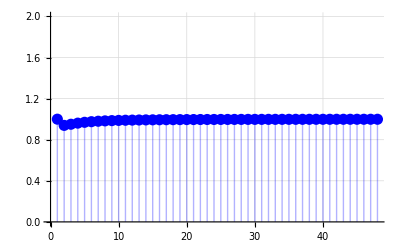

```mathematica
ListPlot[Table[x[n],{n,3,50}],PlotStyle->Directive[PointSize[0.02],Blue],PlotRange->{0,2},GridLines->Automatic,Filling->Axis]
```

```mathematica
L=Limit[x[n],n->∞];
Print["Limit of sequence x_n is, as expected, ",L]
```

Limit of sequence x_n is, as expected, 1

### 9.3. Limit of functions

Task: Given , find . Make sure values of function approaches to  when  approaches  by building a table of values around .

```mathematica
Clear[f,x]
f[x_]=(1-Cos[2x]+(Tan[x])^2)/(x Sin[3x]);
x0=0;
y0=Limit[f[x],x->x0];
Print["Limit of f(x) as x approaches 0 is ",N[y0]]
```

Limit of f(x) as x approaches 0 is 1.

```mathematica
imax=10;
dx=Sort[Table[(-1)^i 10^(-Floor[i/2]),{i,0,imax}]];
Table[N[{x0+dx[[i]],f[x0+dx[[i]]]}],{i,1,imax}]//TableForm
```

-1. | 27.2227
-0.1 | 1.01517
-0.01 | 1.00015
-0.001 | 1.
-0.0001 | 1.
0.00001 | 1.
0.0001 | 1.
0.001 | 1.
0.01 | 1.00015
0.1 | 1.01517

### 9.4. Limit of rational function at special point

Task: Given rational function , find limit . Make sure  is a critical point of . Make sure values of function  approaches  as  approaches  by plotting .

```mathematica
Clear[f,x]
f[x_]=(x^3+4 x^2+5x+2)/(x^3-3x-2);
x0=-1;
y0=Limit[f[x],x->x0];
Print["Limit of f(x) as x approaches -1 is ",y0]
```

Limit of f(x) as x approaches -1 is -1/3

```mathematica
imax=10;
dx=Sort[Table[(-1)^i 10^(-Floor[i/2]),{i,0,imax}]];
Table[N[{x0+dx[[i]],f[x0+dx[[i]]]}],{i,1,imax}]//TableForm
```

-2. | 0.
-1.1 | -0.290323
-1.01 | -0.328904
-1.001 | -0.332889
-1.0001 | -0.333289
-0.99999 | -0.333338
-0.9999 | -0.333378
-0.999 | -0.333778
-0.99 | -0.337793
-0.9 | -0.37931

```mathematica
p1=ListPlot[{{x0,y0}}->{"Critical point"},PlotStyle->{Black,PointSize[0.03]}];
p2=ListPlot[{{x0,y0}},PlotStyle->{White,PointSize[0.015]}];
pf=Plot[f[x],{x,x0-2,x0+2},PlotStyle->Thickness[0.01],PlotTheme->"Scientific"];
Show[pf,p1,p2,AxesOrigin->{0,0},GridLines->Automatic]
```

-Graphics-

### 9.5. Calculating derivatives

Task: Given  find . Build  and . Find value of derivative at .

```mathematica
y[x_]=(1+x^2)/(2Sqrt[1+2 x^2]);
y1[x_]=Simplify[D[y[x],x]];
Print["Derivative of ", y[x]," is ",y1[x]]
```

Derivative of (1+x^2)/(2 √(1+2 x^2)) is x^3/((1+2 x^2)^(3/2))

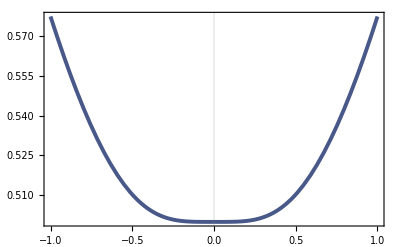

```mathematica
Plot[y[x],{x,-1,1},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

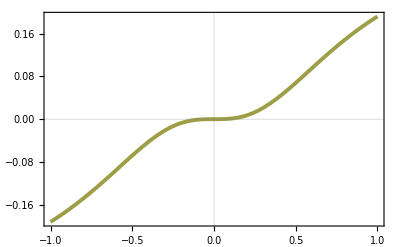

```mathematica
Plot[y1[x],{x,-1,1},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

```mathematica
Print["Derivatives at x=0,0.5,3.0 are ", y1[{0,0.5,3.0}]]
```

Derivatives at x=0,0.5,3.0 are {0,0.0680414,0.326012}

### 9.6. Derivatives of expressions containing trigonometric functions

Task: Find derivative of  and plot its function.

```mathematica
y[x_]=8Sin[1/Tan[3]]+1/5 (Sin[5x])^2/Cos[10x];
y1[x_]=Simplify[D[y[x],x]];
Print["Derivative of ",y[x]," is ",y1[x]]
```

Derivative of 1/5 Sec[10 x] Sin[5 x]^2+8 Sin[Cot[3]] is Sec[10 x] Tan[10 x]

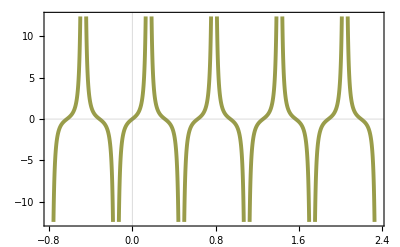

```mathematica
Plot[y1[x],{x,-π/4,(3π)/4},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

### 9.7. Derivatives of higher degrees

Task. Find 4^th order derivative of  and plot it.

```mathematica
y[x_]=Sin[2+3x]Exp[1-2x];
y4[x_]=Simplify[D[y[x],{x,4}]];
Print["4^th order derivative of ",y[x]," is ",y4[x]]
```

4^th order derivative of ⅇ^(1-2 x) Sin[2+3 x] is ⅇ^(1-2 x) (120 Cos[2+3 x]-119 Sin[2+3 x])

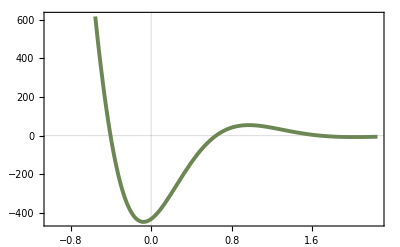

```mathematica
Plot[y4[x],{x,-1,2.25},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

### 9.8. Using derivatives in equations

Task: Show that function  satisfies .

```mathematica
y[x_]=(1-x)/(1+x);
y1[x_]=Simplify[D[y[x],x]];
Print["Derivative of ",y[x]," is ",y1[x]]
```

Derivative of (1-x)/(1+x) is -2/(1+x)^2

```mathematica
Simplify[y[x]-x y1[x]==1+x^2 y1[x]]
```

True

## 10. Using Differential Calculus

### 10.1. Tangent line

Task: Given curve , write equation of tangent at . Plot this curve and tangent line.

```mathematica
y[x_]=2 x^2+3;
y1[x_]=Simplify[D[y[x],x]];
x0=-1;
τ[x_]=y[x0]+y1[x0](x-x0);
Print["Equation of tangent is y(x)=",τ[x]]
```

Equation of tangent is y(x)=5-4 (1+x)

```mathematica
p1=Plot[y[x],{x,-3,2},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"];
p2=Plot[τ[x],{x,x0-1,x0+1},PlotStyle->{Red,Thickness[0.01],Dashed}];
p3=ListPlot[{{x0,y[x0]}}->{"Given point"},PlotStyle->{Blue,PointSize[0.03]}];
Show[p1,p2,p3,PlotRange->All,GridLines->Automatic]
```

-Graphics-

### 10.2. Tangent line and normal for a parametric curve

Task: Given parameterically defined curve , find tangent and normal line equations at . Build these lines and curve, display considered point.

```mathematica
x[t_]=Sin[t]/(1+t^4); x1[t_]=Simplify[D[x[t],t]];
y[t_]=Cos[t]/(1+t^4); y1[t_]=Simplify[D[y[t],t]];
t0=N[π/12];
xτ[t_]=x[t0]+t x1[t0];
yτ[t_]=y[t0]+t y1[t0];
Print["Tangent line has a parametric equation x(t)=",xτ[t]," and y(t)=",yτ[t]]
```

Tangent line has a parametric equation x(t)=0.257609+0.943006 t and y(t)=0.96141-0.32629 t

```mathematica
xn[t_]=x[t0]+t y1[t0];
yn[t_]=y[t0]-t x1[t0];
Print["Normal has a parametric equation x(t)=",xn[t]," and y(t)=",yn[t]]
```

Normal has a parametric equation x(t)=0.257609-0.32629 t and y(t)=0.96141-0.943006 t

```mathematica
p1=ParametricPlot[{x[t],y[t]},{t,-π,π},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"];
p2=ListPlot[{{x[t0],y[t0]}}->{"Considered point"},PlotStyle->{Red,PointSize[0.03]}];
pτ=ParametricPlot[{xτ[t],yτ[t]},{t,-0.5,0.5},PlotStyle->{Blue,Dashed,Thickness[0.007]}];
pn=ParametricPlot[{xn[t],yn[t]},{t,-0.5,0.5},PlotStyle->{Green,Dotted,Thickness[0.007]}];
Show[p1,pτ,pn,p2,PlotRange->All,GridLines->Automatic]
```

-Graphics-

### 10.3. Asymptotes

Task. Find asymptotes of function . Plot this function and its asymptotes.

```mathematica
f[x_]=(3 x^2-7)/(2x+1);
a=Limit[f[x]/x,x->∞];
b=Limit[f[x]-a x,x->∞];
y[x_]=a x+b;
Print["Equation of asymptote is y(x)=",y[x]]
```

Equation of asymptote is y(x)=-3/4+(3 x)/2

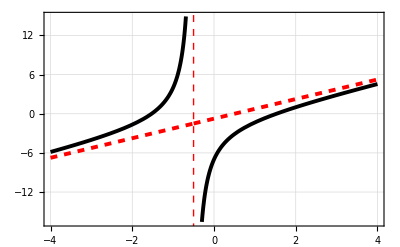

```mathematica
verticalLine=Line[{{-1/2,-20},{-1/2,20}}];
p1=Plot[{f[x],y[x]},{x,-4,4},PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Red,Thickness[0.007],Dashed}},GridLines->Automatic,Epilog->{Directive[{Thick,Red,Dashed}],verticalLine}]
```

### 10.4. Normal and tangent line to a curve defined unexplicitly

Task. Find tangent and normal line equations for . Plot this curve and line equations for arbitrary chosen point.

```mathematica
Φ[x_,y_]=12 x^2+26x y+12 y^2-52x-48y+73;
pΦ=ContourPlot[Φ[x,y]==0,{x,2,6},{y,-5,0},ContourStyle->{Black,Thickness[0.01]}];
x0=4;
sol=Solve[Φ[x0,y] == 0,y];
y0=N[sol[[2]][[1,2]]];
Print["We consider point (",x0,",",y0,")"]
```

We consider point (4,-1.5)

```mathematica
τ=Derivative[1,0][Φ][x0,y0](x-x0)+Derivative[0,1][Φ][x0,y0](y-y0);
n=Derivative[1,0][Φ][x0,y0](y-y0)-Derivative[0,1][Φ][x0,y0](x-x0);
pLines=ContourPlot[{τ==0,n==0},{x,x0-2,x0+2},{y,y0-2,y0+2},ContourStyle->{{Blue,Dashed},{Green,Dashed}}];
pPoint=ListPlot[{{x0,y0}}->{"Considered point"},PlotStyle->{Red,PointSize[0.03]}];
Show[pΦ,pLines,pPoint,AspectRatio->Automatic,GridLines->Automatic]
```

-Graphics-

### 10.5. Maximum and minimum points

Task: Find maximum and minimal values of  on the interval . Plot this function and find max and min using derivatives. Check this solution using function that solve this equation automatically.

```mathematica
f[x_]=(x^5-3x)/Sqrt[16+x^4];
a=-1.5;b=5.5;
s=NSolve[f'[x]==0,x,Reals]
```

{{x→-0.867639},{x→0.867639}}

```mathematica
x0=N[s[[1]][[1,2]]];
y0=f[x0];
P0={x0,y0};
Print["We will consider a critical point ",P0]
```

We will consider a critical point {-0.867639,0.5187}

```mathematica
f2[x_]=Simplify[D[f[x],x,{x,2}]];
secondDerivative0=f2[x0];
Print["Second  derivative at point ",P0," is ",secondDerivative0]
```

Second  derivative at point {-0.867639,0.5187} is 10.5986

Thus we see that  which means we have a local minima.

```mathematica
intervalValues={f[a],f[b]};
Print["Values on the edge of interval are ",intervalValues]
```

Values on the edge of interval are {-0.674109,164.399}

Therefore, we see that the maximum value occurs at  where  whereas minimum at  where . Value at our critical point equals  which is neither maximum nor minimum.

```mathematica
p1=Plot[f[x],{x,a-0.3,b+0.2},PlotStyle->Red];
pPoint=ListPlot[{{a,f[a]},{b,f[b]},{x0,f[x0]}}->{"Min","Max","Extremum"},PlotStyle->{Blue,PointSize[0.015]}];
Show[p1,pPoint,GridLines->Automatic]
```

-Graphics-

```mathematica
mn=Minimize[{f[x],a<=x<=b},x]
mx=Maximize[{f[x],a<=x<=b},x]
```

{-0.674109,{x→-1.5}}

{164.399,{x→5.5}}

### 10.6. Partial Derivatives

Task. Find first and second order partial derivatives of . Plot function and normal vector at .

```mathematica
z[x_,y_]=(x^2-y^2)/(1+x^2);
zx[x_,y_]=Simplify[D[z[x,y],x]];
zy[x_,y_]=Simplify[D[z[x,y],y]];
Print["First order derivatives are: ",{zx[x,y],zy[x,y]}]
```

First order derivatives are: {(2 x (1+y^2))/((1+x^2)^2),-(2 y)/(1+x^2)}

```mathematica
zxx[x_,y_]=Simplify[D[z[x,y],{x,2}]];
zxy[x_,y_]=Simplify[D[z[x,y],x,y]];
zyy[x_,y_]=Simplify[D[z[x,y],{y,2}]];
Print["Second order derivatives are: ",{zxx[x,y],zxy[x,y],zyy[x,y]}]
```

Second order derivatives are: {-(2 (-1+3 x^2) (1+y^2))/((1+x^2)^3),(4 x y)/((1+x^2)^2),-2/(1+x^2)}

```mathematica
x0=-0.5;y0=0.7;
P={x0,y0,z[x0,y0]};
Print["Considered point has coordinates ",P]
```

Considered point has coordinates {-0.5,0.7,-0.192}

```mathematica
n=-{zx[x0,y0],zy[x0,y0],-1};
Print["Normal vector has coordinates ",n]
p1=Plot3D[z[x,y],{x,-1,1},{y,-1,1},PlotRange->All,ColorFunction->"DarkRainbow",PlotStyle->Opacity[0.7]];
pt=ListPointPlot3D[{P}->"Point",PlotStyle->{Red,PointSize[0.05]}];
p2=Graphics3D[{Red,Thickness[0.02],Arrowheads[0.05],Arrow[{P,P+n}]}];
Show[p1,p2,pt,BoxRatios->{1,1,1},AxesLabel->{"x","y","z"}]
```

Normal vector has coordinates {0.9536,1.12,1}

-Graphics3D-

## 11. Definite and indefinite integrals. Multiple integrals.

### 11.1. Calculating indefinite integrals.

Task: Calculate indefinite integral . Build plot of an integrand and antiderivative.

```mathematica
f[x_]=Exp[-3x](2-9x);
F[x_]=Integrate[f[x],x];
Print["Integral equals ",F[x]]
```

Integral equals ⅇ^(-3 x) (1/3+3 x)

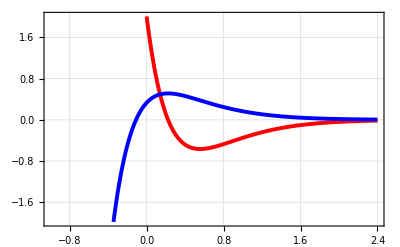

```mathematica
Plot[{f[x],F[x]},{x,-1,2.4},PlotTheme->"Scientific",PlotStyle->{{Red,Thickness[0.007]},{Blue,Thickness[0.007]}},GridLines->Automatic]
```

### 11.2. Indefinite integral of arbitrary functions

Task: Calculate indefinite integral . Build integrand and antiderivative plots.

```mathematica
f[x_]=(x^3+3)/(x^4+1);
F[x_]=Simplify[∫f[x]ⅆx];
Print["Integral equals to ",F[x]]
```

Integral equals to 1/8 (-6 √2 ArcTan[1-√2 x]+6 √2 ArcTan[1+√2 x]-3 √2 Log[1-√2 x+x^2]+3 √2 Log[1+√2 x+x^2]+2 Log[1+x^4])

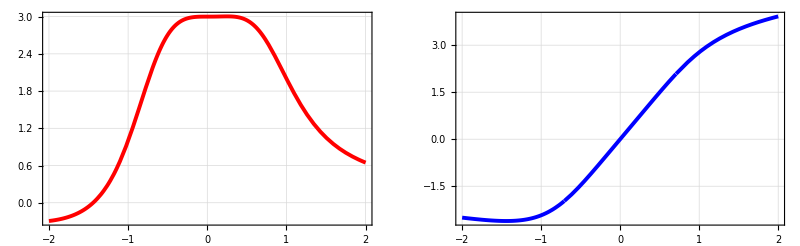

```mathematica
p1=Plot[f[x],{x,-2,2},PlotTheme->"Scientific",PlotStyle->{Red,Thickness[0.007]},GridLines->Automatic];
p2=Plot[F[x],{x,-2,2},PlotTheme->"Scientific",PlotStyle->{Blue,Thickness[0.007]},GridLines->Automatic];
GraphicsRow[{p1,p2}]
```

### 11.3. Indefinite integral of rational functions

Task: Calculate indefinite integral 	. Plot integrand and its antiderivative, excluding special points

```mathematica
f[x_]=(x^3-6 x^2+10x-10)/((x+1)(x-2)^3);
q[x_]=Apart[f[x]];
Print["After expanding fraction into simpler fractions, we get ",q[x]]
```

After expanding fraction into simpler fractions, we get -2/(-2+x)^3+1/(1+x)

```mathematica
F[x_]=Integrate[q[x],x];
Print["Integral equals ",F[x]]
```

Integral equals 1/(-2+x)^2+Log[1+x]

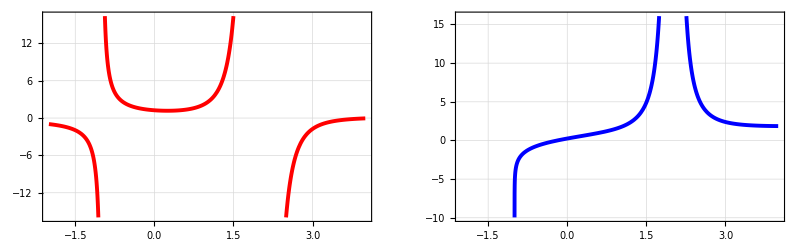

```mathematica
p1=Plot[f[x],{x,-2,4},PlotTheme->"Scientific",PlotStyle->{Red,Thickness[0.007]},GridLines->Automatic];
p2=Plot[F[x],{x,-2,4},PlotTheme->"Scientific",PlotStyle->{Blue,Thickness[0.007]},GridLines->Automatic];
GraphicsRow[{p1,p2}]
```

### 11.4. Definite integrals.

Task: Calculate definite integral . Plot integrand and highlight an integrated area.

```mathematica
f[x_]=(x^2+2x+1)Exp[-x^2];
a=0;b=2;
s=N[Integrate[f[x],{x,a,b}]];
Print["Value of integral is ",s]
```

Value of integral is 2.28649

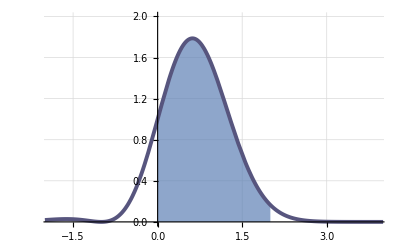

```mathematica
p1=Plot[f[x],{x,a,b},Filling->Axis,FillingStyle->Opacity[0.7],PlotRange->{0,8}];
p2=Plot[f[x],{x,a-2,b+2},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"];
Show[p1,p2,PlotRange->{{a-1.9,b+1.9},{0,2}},AxesOrigin->{0,0},GridLines->Automatic]
```

### 11.5. Definite Integrals of arbitrary functions

Task: Find definite integral . Plot integrand and area of integration.

```mathematica
f[x_]=(x-(ArcTan[x])^4)/(1+x^2);
a=0;b=Sqrt[3];
s=Integrate[f[x],{x,a,b}];
Print["Integral equals ",s," and numerically ",N[s,3]]
```

Integral equals -π^5/1215+Log[2] and numerically 0.441

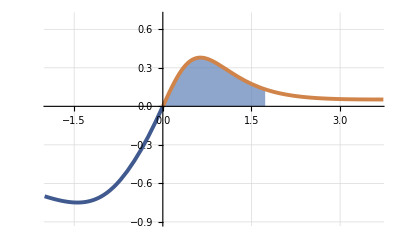

```mathematica
p1=Plot[f[x],{x,a,b},Filling->Axis,FillingStyle->Opacity[0.7],PlotRange->{0,8}];
p2=Plot[f[x],{x,a-2,b+2},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"];
Show[p1,p2,PlotRange->{{a-1.9,b+1.9},{-0.9,0.7}},AxesOrigin->{0,0},GridLines->Automatic]
```

### 11.6. Definite integrals of trigonometric functions

Task: Calculate integral . Plot integrand and area of integration,

```mathematica
f[x_]=2^8(Sin[x])^4(Cos[x])^4;
a=π/2;b=π;
s=Integrate[f[x],{x,a,b}];
Print["Value of this integral is ",s]
```

Value of this integral is 3 π

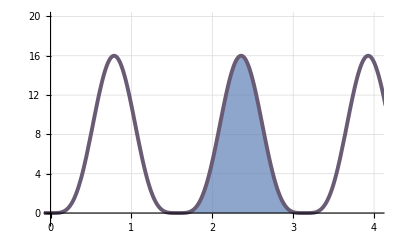

```mathematica
p1=Plot[f[x],{x,a,b},Filling->Axis,FillingStyle->Opacity[0.7],PlotRange->{0,30}];
p2=Plot[f[x],{x,-2,b+1},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"];
Show[p1,p2,PlotRange->{{0,b+0.9},{-0.9,20.0}},AxesOrigin->{0,0},GridLines->Automatic]
```

### 11.7. Multiple Integral

Task: Calculate double integral  for region . Plot region .

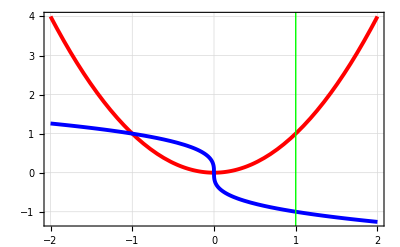

```mathematica
y1[x_]=x^2;
y2[x_]=-CubeRoot[x];
l=Line[{{1,-10},{1,10}}];
p1=Plot[{y1[x],y2[x]},{x,-2,2},PlotTheme->"Scientific",PlotStyle->{{Red,Thickness[0.007]},{Blue,Thickness[0.007]}},GridLines->Automatic,Epilog->{Directive[{Thick,Green}],l}]
```

Therefore, we see that region  is bounded between  and

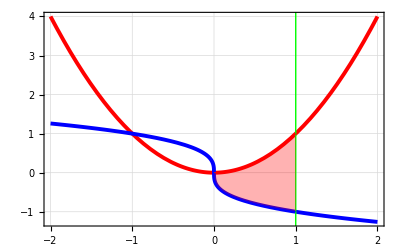

```mathematica
p2=Plot[{y1[x],y2[x]},{x,0,1},PlotTheme->"Scientific",PlotStyle->{{Red,Thickness[0.002]},{Blue,Thickness[0.002]}},Filling->{1->{2}},GridLines->Automatic];
Show[p1,p2]
```

That being said, we can rewrite our integral as .

```mathematica
f[x_,y_]=4/5 x y+9/11 x^2 y^2;
s=Integrate[f[x,y],{x,0,1},{y,-CubeRoot[x],x^2}];
Print["Integral equals ",s]
```

Integral equals 1/66

### 11.8. Calculating double integrals

Task: Evaluate integral  for region .

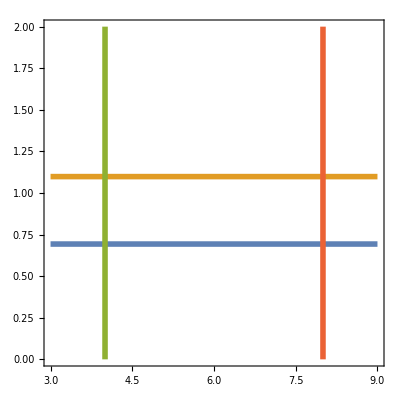

```mathematica
p1=ContourPlot[{y==Log[2],y==Log[3],x==4,x==8},{x,3,9},{y,0,2},ContourStyle->Thickness[0.01]]
```

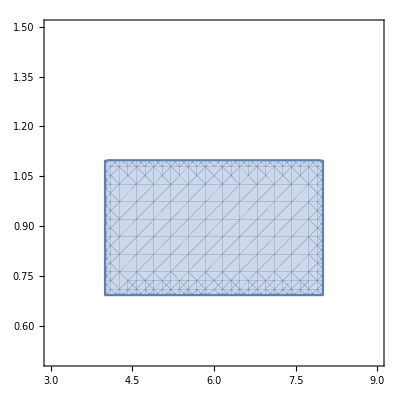

```mathematica
p2=RegionPlot[y>=Log[2]&&y<=Log[3]&&x>=4&&x<=8,{x,3,9},{y,0.5,1.5}]
```

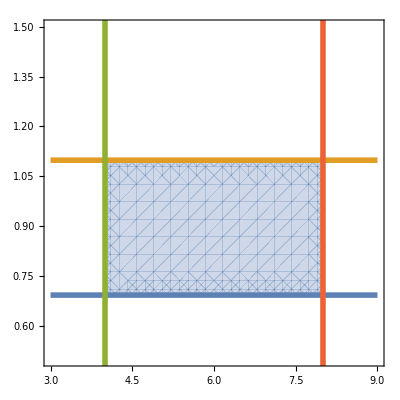

```mathematica
Show[p2,p1]
```

Therefore, our integral becomes .

```mathematica
f[x_,y_]=y Exp[(x y)/4];
F=Chop[∫_4^8 ∫_Log[2]^Log[3] f[x,y]ⅆyⅆx];
Print["Value of integral is ",F]
```

Value of integral is 6

## 12. Integral Calculus Application

### 12.1. Area between two explicitly defined curves

Task: Find area of region bounded by two curves , between their two intersection points. Plot these curves and target area.

```mathematica
f1[x_]=Sqrt[2-x];
f2[x_]=(x+1)Sqrt[2-x];
s=Solve[f1[x]==f2[x],x,Reals];
x1=x/.s[[1]];
x2=x/.s[[2]];
Print["Two intersection points are ",x1," and ",x2]
```

Two intersection points are 0 and 2

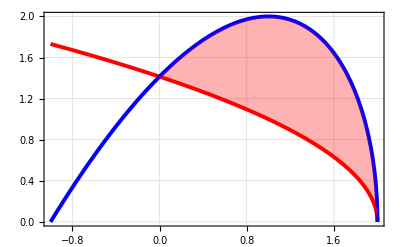

```mathematica
p1=Plot[{f1[x],f2[x]},{x,-1,2},PlotTheme->"Scientific",PlotStyle->{{Red,Thickness[0.007]},{Blue,Thickness[0.007]}},GridLines->Automatic];
p2=Plot[{f1[x],f2[x]},{x,0,2},PlotTheme->"Scientific",PlotStyle->{{Red,Thickness[0.002]},{Blue,Thickness[0.002]}},Filling->{1->{2}},GridLines->Automatic];
Show[p1,p2]
```

```mathematica
s=Integrate[f2[x]-f1[x],{x,x1,x2}];
Print["Area of region equals ",s]
```

Area of region equals (16 √2)/15

### 12.2. Finding length of explicitly defined curve

Task: Find length of a curve segment . Build a curve and display segment on it.

```mathematica
y[x_]=Exp[x];
x1=Log[Sqrt[15]];x2=Log[Sqrt[24]];
L=∫_x1^x2 √(1+y'[x]^2)ⅆx;
Print["Length of a segment is ",L]
```

Length of a segment is 1+ArcTanh[4]-ArcTanh[5]

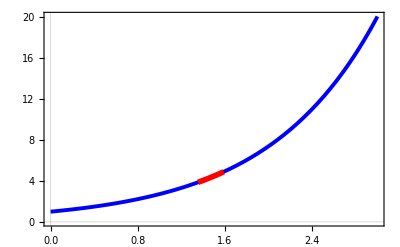

```mathematica
p1=Plot[y[x],{x,0,3},PlotTheme->"Scientific",PlotStyle->{Blue,Thickness[0.007]}];
p2=Plot[y[x],{x,x1,x2},PlotTheme->"Scientific",PlotStyle->{Red,Thickness[0.01]},GridLines->Automatic];
Show[p1,p2]
```

### 12.3. Finding length of a parametric curve

Task: Find length of curve . Plot this segment.

```mathematica
x[t_]=5/2(t-Sin[t]);
y[t_]=5/2(1-Cos[t]);
a=0;b=2π;
L=Integrate[Sqrt[D[x[t],t]^2+D[y[t],t]^2],{t,a,b}];
Print["Length of this segment is ",L]
```

Length of this segment is 20

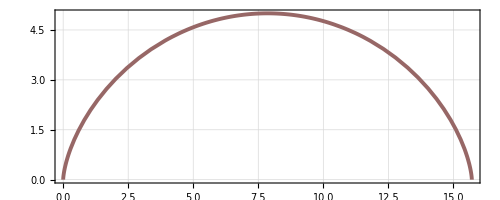

```mathematica
ParametricPlot[{x[t],y[t]},{t,0,2π},PlotTheme->"Scientific",ColorFunction->"Rainbow",PlotStyle->{Thickness[0.007],Blue},GridLines->Automatic]
```

### 12.4. Finding plate’s mass

Task: Given plate’s surface density  and region it takes on a plane , display it and find its mass.

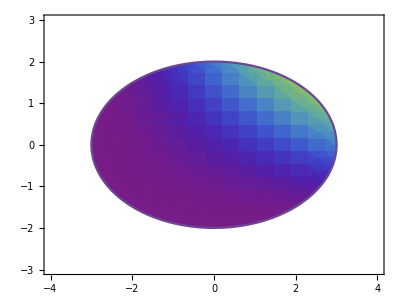

```mathematica
R=x^2/9+y^2/4<=1;
μ[x_,y_]=x^2 y^2;
RegionPlot[R,{x,-4,4},{y,-3,3},AspectRatio->Automatic,ColorFunction->Function[{x,y},ColorData["Rainbow"][μ[x,y]]]]
```

```mathematica
mass=Integrate[μ[x,y] Boole[R],{x,-4,4},{y,-3,3}];
Print["Plate's mass is ",mass]
```

Plate's mass is 9 π

### 12.5. Finding body’s volume

Task: Find volume of body  and display it.

```mathematica
Clear[x,y,z]
R=(4<=x^2+y^2+z^2<=49)&&(-Sqrt[3]x<y<Sqrt[3]x)&&(z>=Sqrt[(x^2+y^2)/99]);
RegionPlot3D[R,{x,-2,8},{y,-2,8},{z,-2,8},PlotPoints->100,Boxed->False,AxesOrigin->{0,0,0},Mesh->None,PlotStyle->Directive[Yellow,Opacity[0.5]]]
```

-Graphics3D-

```mathematica
v=Chop[NIntegrate[Boole[R],{x,-∞,+∞},{y,-∞,+∞},{z,-∞,+∞}]];
Print["Value of integral is ",v]
```

Value of integral is 210.487

## 13. Interpolation and approximation

### 13.1. Curved lines

Task: Build a curved line consisting of vertices  using ListPlot, Bernstein’s formula and Interpolation.

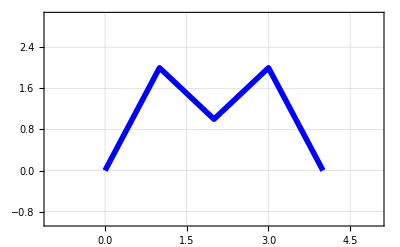

```mathematica
A={{0,0},{1,2},{2,1},{3,2},{4,0}};
ListPlot[A,PlotRange->{{-1,5},{-1,3}},PlotStyle->{Thickness[0.01],Blue},Joined->True,GridLines->Automatic,PlotTheme->"Scientific"]
```

Bernstein formula gives an equation 4-3/2 Abs[-3+x]+Abs[-2+x]-3/2 Abs[-1+x]

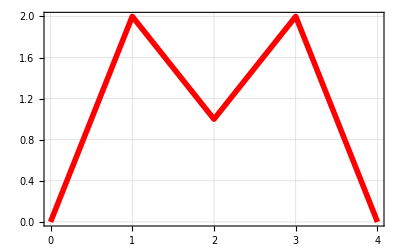

```mathematica
n=Length[A];
y[x_]=Simplify[1/2(A[[1,2]]+(A[[2,2]]-A[[1,2]])/(A[[2,1]]-A[[1,1]])(x-A[[1,1]])+A[[n-1,2]]+(A[[n,2]]-A[[n-1,2]])/(A[[n,1]]-A[[n-1,1]])(x-A[[n-1,1]]))+1/2 Sum[((A[[k+1,2]]-A[[k,2]])/(A[[k+1,1]]-A[[k,1]])-(A[[k,2]]-A[[k-1,2]])/(A[[k,1]]-A[[k-1,1]]))Abs[x-A[[k,1]]],{k,2,n-1}]];
Print["Bernstein formula gives an equation ",y[x]]
Plot[y[x],{x,0,4},GridLines->Automatic,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.01],Red]]
```

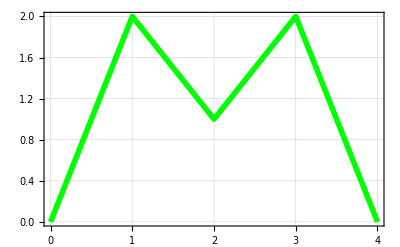

```mathematica
Plot[Interpolation[A,InterpolationOrder->1][x],{x,0,4},GridLines->Automatic,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.01],Green]]
```

### 13.2. Piecewise function

Task. Plot a piecewise function.

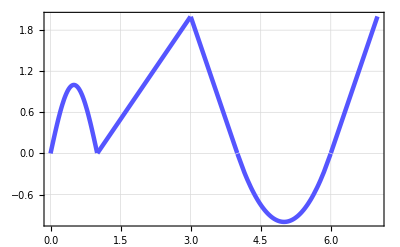

```mathematica
y[x_]=Piecewise[{{0,x<=0},{Sin[π x],0<=x<=1},{x-1,1<=x<=3},{8-2x,3<=x<=4},{(x-4)(x-6),4<=x<=6},{2x-12,x>=6}}];
Plot[y[x],{x,0,7},GridLines->Automatic,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.008],Lighter[Blue]]]
```

### 13.3. Polynomial interpolation of a set of points

Task. You are given a set of points on a plane. Plot an interpolation polynomial: {1,3}, {2,1}, {5,3}, {6,5}, {8,2}, {9,4}, {11,2}.

```mathematica
A={{1,3},{2,1},{5,3},{6,5},{8,2},{9,4},{11,2}};
P[x_]=Expand[InterpolatingPolynomial[A,x]];
Print["Interpolation polynomial is P(x)=",P[x]]
```

Interpolation polynomial is P(x)=-1049/42+(26251 x)/432-(293773 x^2)/6480+(76127 x^3)/5184-(3989 x^4)/1728+(901 x^5)/5184-(911 x^6)/181440

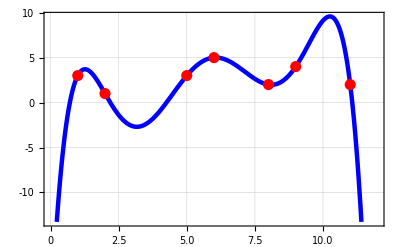

```mathematica
Plot[P[x],{x,0,12},PlotStyle->{Thickness[0.008],Blue},PlotTheme->"Business",Epilog->{Red,PointSize[0.02],Point/@A},GridLines->Automatic]
```

### 13.4. Polynomial interpolation of a function

Task. On a segment [-1,1] approximate a function f(x)=ln(x^2+1)/(x^2+1) using interpolation polynomial.

```mathematica
f[x_]=Log[x^2+1]/(x^2+1);
ts = Chop[Table[{x,f[x]},{x,-1,1,0.2}]];
P[x_]=Chop[Collect[InterpolatingPolynomial[ts,x],x]];
Print["Obtained polynomial is ",P[x]]
```

Obtained polynomial is 0.999387 x^2-1.47693 x^4+1.60522 x^6-1.15805 x^8+0.376936 x^10

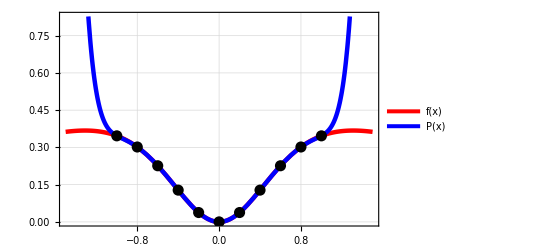

```mathematica
Plot[{f[x],P[x]},{x,-1.5,1.5},PlotStyle->{{Thickness[0.008],Red},{Thickness[0.008],Blue}},Epilog->{Black,PointSize[0.02],Point/@ts},GridLines->Automatic,PlotTheme->"Business",PlotLegends->{"f(x)","P(x)"}]
```

### 13.5. Polynomial interpolation of a parametric function

Task. On a given interval [Pi,2Pi] with a step Pi/4 try to approximate a parametric function: x=t*cos(t),y=t*sin(t)/4.

```mathematica
x[t_]=t Cos[t];y[t_]=(t Sin[t])/4;
a=π;b=2π;step=π/4;
pnts=Table[{x[t],y[t]},{t,a,b,step}];
P[x_]=N[Chop[Collect[InterpolatingPolynomial[pnts,x],x]]];
Print["Polynomial P(x)=",P[x]]
```

Polynomial P(x)=-1.1781+0.440171 x+0.00069317 x^2-0.0570858 x^3+0.0080493 x^4

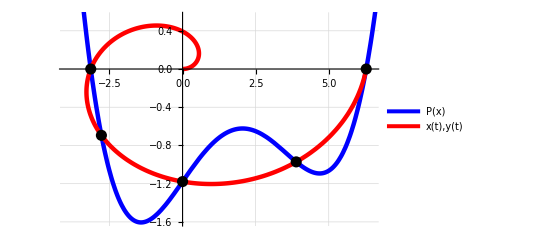

```mathematica
Show[
Plot[P[x],{x,-4,10},PlotStyle->{Thickness[0.008],Blue},PlotLegends->{"P(x)"}],
ParametricPlot[{x[t],y[t]},{t,0,2Pi},PlotStyle->{Thickness[0.008],Red},PlotLegends->{"x(t),y(t)"},PlotTheme->"Scientific"],
PlotRange->{{-4,6.5},{-1.6,0.55}},Epilog->{Black,PointSize[0.02],Point/@pnts},GridLines->Automatic
]
```

### 13.6. Polynomial interpolation of non-explicitly defined function

Task. On an interval [-10,2] with a step size of 4 approximate a non-explicitly defined function using interpolation polynomial of degree 3

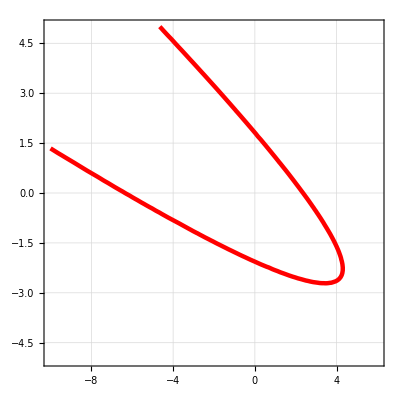

```mathematica
F[x_,y_]=x^2+4x y+4 y^2+4x+y-15;
Fp=ContourPlot[F[x,y]==0,{x,-10,6},{y,-5,5},ContourStyle->{Red,Thickness[0.008]},PlotTheme->"Scientific",GridLines->Automatic]
```

```mathematica
X=Table[x,{x,-10,2,4}];
pnts=Table[{X[[i]],N[y/.Solve[F[X[[i]],y]==0,y][[1]]]},{i,1,Length[X]}];
Print["We have a set of points ",pnts]
```

We have a set of points {{-10,1.33726},{-6,-0.127603},{-2,-1.47354},{2,-2.54473}}

```mathematica
P[x_]=N[Chop[Collect[InterpolatingPolynomial[pnts,x],x]]];
Print["Interpolation polynomial is ",P[x]]
```

Interpolation polynomial is -2.05321-0.269421 x+0.0110204 x^2+0.000405774 x^3

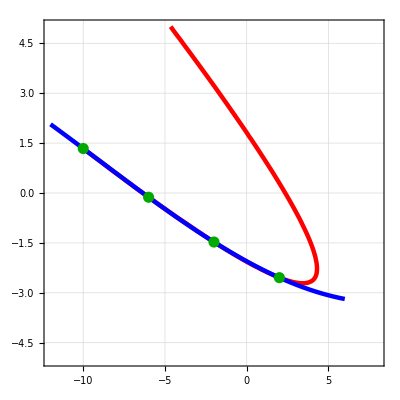

```mathematica
Pp=Plot[P[x],{x,-12,6},PlotStyle->{Thickness[0.008],Blue}];
Show[Fp,Pp,PlotRange->{{-12,8},{-5,5}},Epilog->{Darker[Green],PointSize[0.02],Point[pnts]},GridLines->Automatic]
```

### 13.7. Hermite Interpolation

Task. Given vertices (-2,-4), (-1,-2), (1,0), (2,0), using Interpolation function build an interpolation cubic polynomial. Also, build a plot of an Hermite polynomial with gi=(1,3,-1,1)

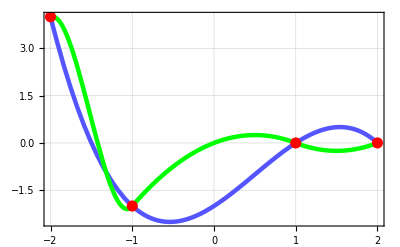

```mathematica
data1={{-2,4},{-1,-2},{1,0},{2,0}};
data2={{{-2},4,1},{{-1},-2,3},{{1},0,-1},{{2},0,1}};
f1=Interpolation[data1,InterpolationOrder->3];
f2=Interpolation[data2,Method->"Hermite",InterpolationOrder->3];
Show[
{Plot[{f1[x],f2[x]},{x,-2,2},PlotTheme->"Scientific",GridLines->Automatic,PlotStyle->{{Lighter[Blue],Thickness[0.008]},{Green,Thickness[0.008]}}],ListPlot[data1,PlotStyle->{PointSize[0.02],Red}]}
]
```

### 13.8. Spline interpolation

Task. Given vertices (0,0), (1,1), (2,-1), (3,0), using Interpolation function build an interpolation cubic polynomial. Also, build a plot of an Spline polynomial.

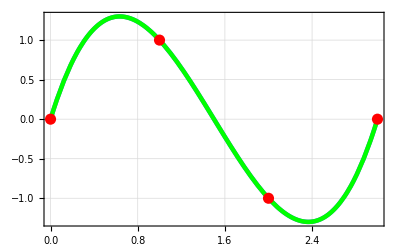

```mathematica
data={{0,0},{1,1},{2,-1},{3,0}};
f1=Interpolation[data,InterpolationOrder->3];
f2=Interpolation[data,Method->"Spline",InterpolationOrder->3];
Show[
{Plot[{f1[x],f2[x]},{x,0,3},PlotTheme->"Scientific",GridLines->Automatic,PlotStyle->{{Lighter[Blue],Thickness[0.008]},{Green,Thickness[0.008]}}],ListPlot[data,PlotStyle->{PointSize[0.02],Red}]}
]
```

### 13.9. Approximation

Task. Given a set of points {0,1},{1,-2},{2,2},{3,3},{4,1},{5,-1}, apply the linear approximation and approximation using basis functions 1,x,cos(x),e^(-x).

```mathematica
data={{0,1},{1,-2},{2,2},{3,3},{4,1},{5,-1}};
line1=Fit[data,{1,x},x];
Print["Linear approximation is ",line1]
```

Linear approximation is 0.666667-1.49702×10^-17 x

```mathematica
line2=Fit[data,{1,x,Cos[x],Exp[-x]},x];
Print["Linear approximation using basis functions is ",line2]
```

Linear approximation using basis functions is -2.09607+6.70458 ⅇ^-x+0.340882 x-3.74427 Cos[x]

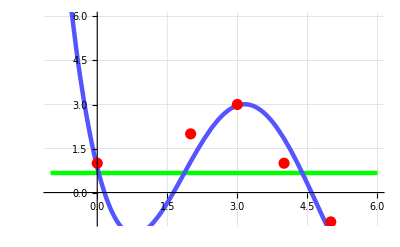

```mathematica
p1=Plot[line1,{x,-1,6},PlotStyle->{Green,Thickness[0.008]}];
p2=Plot[line2,{x,-1,6},PlotStyle->{Lighter[Blue],Thickness[0.008]}];
p3=ListPlot[data,PlotStyle->{PointSize[0.02],Red}];
Show[p1,p2,p3,PlotRange->{-1,6},PlotTheme->"Business",GridLines->Automatic]
```

## 14. Solving Differential Equations

### 14.1. First order differential equations

Task: Using DSolve, find integral curve of the differential equation  passing through .

```mathematica
Remove[x,y];
r=DSolve[{y'[x]==x y[x],y[0]==-1},y[x],x];
y[x_]=Simplify[y[x]/.r[[1]]];
Print["Solution to differential equation y'=xy is ",y[x]]
```

Solution to differential equation y'=xy is -ⅇ^(x^2/2)

```mathematica
p1=Plot[y[x],{x,-2,2},PlotStyle->{Blue,Thickness[0.008]},PlotTheme->"Scientific",GridLines->Automatic];
p2=ListPlot[{{0,-1}}->{"M"},PlotStyle->{Red,PointSize[0.03]}];
Show[p1,p2,PlotRange->{{-1.3,1.3},{-3,0}}]
```

-Graphics-

### 14.2. Second order differential equations with constant coefficients

Task: Using DSolve, find the general solution to DE . Set to arbitrary constants values  and build a plot for this particular case.

```mathematica
Remove[x,y];
r=DSolve[y''[x]+2y'[x]==10Exp[x](Sin[x]+Cos[x]),y[x],x]
```

{{y[x]→-1/2 ⅇ^(-2 x) C[1]+C[2]-ⅇ^x Cos[x]+3 ⅇ^x Sin[x]}}

```mathematica
f=y[x]/.r[[1]];
Print["Solution to the given DE is ",f]
```

Solution to the given DE is -1/2 ⅇ^(-2 x) C[1]+C[2]-ⅇ^x Cos[x]+3 ⅇ^x Sin[x]

```mathematica
y[x_]=f/.{C[1]->1,C[2]->-1};
Print["When C_1=1,C_2=-1 we obtain ",y[x]]
```

When C_1=1,C_2=-1 we obtain -1-ⅇ^(-2 x)/2-ⅇ^x Cos[x]+3 ⅇ^x Sin[x]

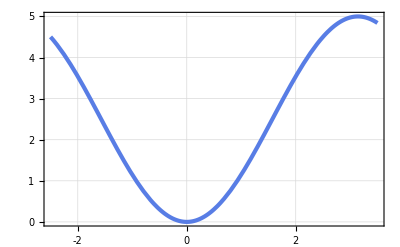

```mathematica
Plot[y[x],{x,-2.5,3.5},PlotTheme->"Business",GridLines->Automatic]
```

### 14.3. Third order differential equation with constant coefficients

Task: Using function DSolve, find general solution of equation . Set all constants to  and plot of solution.

```mathematica
Remove[x,y,r,f];
r=DSolve[y'''[x]-y''[x]-2y'[x]==(6x-11)Exp[-x],y[x],x];
yc[x_]=y[x]/.r[[1]];
y[x_]=yc[x]/.{C[1]->1,C[2]->1,C[3]->1};
Print["Answer to the given question is ",y[x]]
```

Answer to the given question is 1+ⅇ^(2 x)/2+ⅇ^-x (-3-x+x^2)

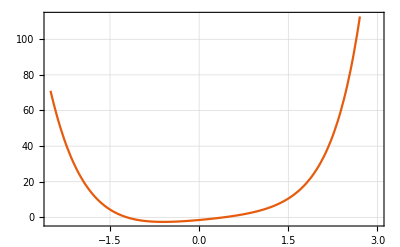

```mathematica
Plot[y[x],{x,-2.5,3},PlotTheme->"Scientific",GridLines->Automatic]
```

### 14.4. Cauchy problem with constant coefficients

Task: Using DSolve, solve and plot a solution to .

```mathematica
Remove[x,y];
r=DSolve[{y''[x]+9y[x]==9/Sin[3x],y[0]==1,y'[0]==0},y[x],x]
```

{}

There are no solutions, hence let us choose different initial conditions

```mathematica
r=DSolve[{y''[x]+9y[x]==9/Sin[3x],y[1]==0,y'[1]==0},y[x],x]
```

{{y[x]→3 Cos[3 x]-3 x Cos[3 x]-Log[Sin[3]] Sin[3 x]+Log[Sin[3 x]] Sin[3 x]}}

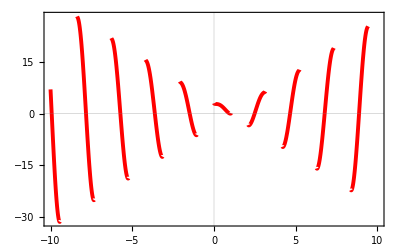

```mathematica
y[x_]=y[x]/.r[[1]];
Plot[y[x],{x,-10,10},PlotStyle->Directive[Thickness[0.007],Red],PlotTheme->"Scientific"]
```

### 14.5. First-order system of differential equations

Task. Using DSolve, find a general solution of a system of differential equations. Set all constants to 1 and plot obtained functions: x’=2x-3y+z,y’=x+4y-z,z’=x-y+2z.

```mathematica
Remove[x,y,z,t,X,Y,Z];
r=DSolve[{x'[t]==2x[t]-3y[t]+z[t],y'[t]==x[t]+4y[t]-z[t],z'[t]==x[t]-y[t]+2z[t]},{x[t],y[t],z[t]},t];
X[t_] = Simplify[x[t]/.r[[1,1]]/.{C[1]->1,C[2]->1,C[3]->1}];
Y[t_] = Simplify[y[t]/.r[[1,2]]/.{C[1]->1,C[2]->1,C[3]->1}];
Z[t_] = Simplify[z[t]/.r[[1,3]]/.{C[1]->1,C[2]->1,C[3]->1}];
Print["Obtained functions are: x(t)=",X[t],", y(t)=",Y[t],", z(t)=",Z[t]]
```

Obtained functions are: x(t)=-ⅇ^(2 t) (1+ⅇ^t (-2+4 t)), y(t)=ⅇ^(2 t) (-1+2 ⅇ^t), z(t)=-ⅇ^(2 t) (3+4 ⅇ^t (-1+t))

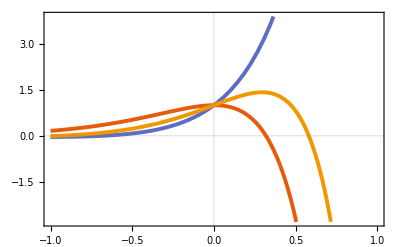

```mathematica
Plot[{X[t],Y[t],Z[t]},{t,-1,1},PlotTheme->"Scientific",PlotStyle->Thickness[0.007]]
```

### 14.6. Cauchy problem for a first-order system of differential equations

Task: Using DSolve function, find solution of a Cauchy problem for a system of differential equations. Plot results. x’=-3x-4y,y’=-2x-y,x(0)=1,y(0)=4

```mathematica
Remove[x,y,t,X,Y];
r=DSolve[{x'[t]==-3x[t]-4y[t],y'[t]==-2x[t]-y[t],x[0]==1,y[0]==4},{x[t],y[t]},t];
X[t_]=Simplify[x[t]/.r[[1,1]]];
Y[t_]=Simplify[y[t]/.r[[1,2]]];
Print["Obtained expressions are: x(t)=",X[t],", y(t)=",Y[t]]
```

Obtained expressions are: x(t)=(10 ⅇ^(-5 t))/3-(7 ⅇ^t)/3, y(t)=(5 ⅇ^(-5 t))/3+(7 ⅇ^t)/3

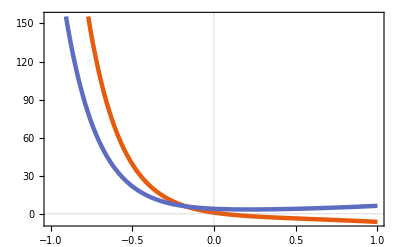

```mathematica
Plot[{X[t],Y[t]},{t,-1,1},PlotTheme->"Scientific",PlotStyle->Thickness[0.008]]
```

### 14.7. Cauchy problem for an inhomogeneous system of differential equations

Task. Using DSolve, find a solution of Cauchy problem and plot it: x’=2x+4y-8,y’=3x+6y,x(0)=-1,y(0)=1.

```mathematica
Remove[x,y,t,X,Y];
r=DSolve[{x'[t]==2x[t]+4y[t]-8,y'[t]==3x[t]+6y[t],x[0]==-1,y[0]==1},{x[t],y[t]},t];
X[t_]=Simplify[x[t]/.r[[1,1]]];
Y[t_]=Simplify[y[t]/.r[[1,2]]];
Print["Obtained expressions are: x(t)=",X[t],", y(t)=",Y[t]]
```

Obtained expressions are: x(t)=-1-6 t, y(t)=1+3 t

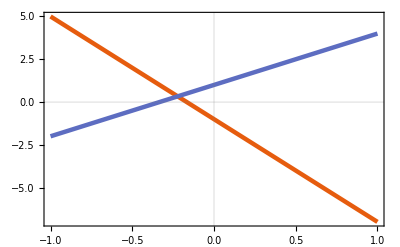

```mathematica
Plot[{X[t],Y[t]},{t,-1,1},PlotTheme->"Scientific",PlotStyle->Thickness[0.008]]
```

### 14.8. Cauchy problem for a second order system of differential equations

Task. Using DSolve, find solution of a Cauchy problem and plot obtained solution: 2x’’+2x’+x+3y’’+y’+y=0,x’’+4x’-x+3y’’+2y’-y=0,x(0)=1,y(0)=0,x’(0)=-1,y’(0)=2

```mathematica
Remove[x,y,t,X,Y];
r=DSolve[{2x''[t]+2x'[t]+x[t]+3y''[t]+y'[t]+y[t]==0,x''[t]+4x'[t]-x[t]+3y''[t]+2y'[t]-y[t]==0,x[0]==1,y[0]==0,x'[0]==-1,y'[0]==2},{x[t],y[t]},t];
X[t_]=Simplify[x[t]/.r[[1,1]]];
Y[t_]=Simplify[y[t]/.r[[1,2]]];
Print["Obtained expressions are: x(t)=",X[t],", y(t)=",Y[t]]
```

Obtained expressions are: x(t)=5-3 ⅇ^t-Cos[t]+2 Sin[t], y(t)=-5+3 ⅇ^t+2 Cos[t]-Sin[t]

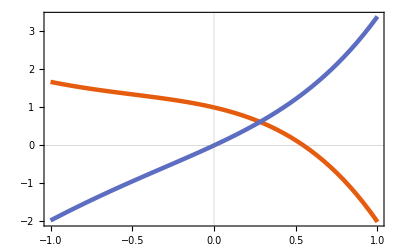

```mathematica
Plot[{X[t],Y[t]},{t,-1,1},PlotTheme->"Scientific",PlotStyle->Thickness[0.008]]
```